Pribljižek števila pi pri 100000 točkah: 3.12768

Razlika realne vrednosti in pribljižka pri 100000 točkah: 0.0139127

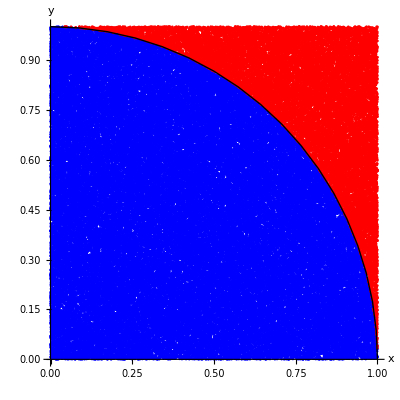

```mathematica
PiAproksimacija[in_]:=Module[{znotrajKroga,x,y,dataZnotraj,dataZunaj},

znotrajKroga=0;
dataZnotraj={};
dataZunaj={};

Do[
x=RandomReal[];
y=RandomReal[];

If[
x^2+y^2<=1,znotrajKroga++;
AppendTo[dataZnotraj,{x,y}],AppendTo[dataZunaj,{x,y}]],{in}];
PI=(4.00 (znotrajKroga/in));

Razlika =Abs[π-PI];

Print["Pribljižek števila pi pri ",in ," točkah: ",PI];
Print["Razlika realne vrednosti in pribljižka pri ",in ," točkah: ",Razlika];

PlotNot=ListPlot[dataZnotraj,PlotStyle->{PointSize[0.005],Blue},PlotRange->{{0,1},{0,1}},AspectRatio->1,AxesLabel->{"x","y"}];

PlotZun=ListPlot[dataZunaj,PlotStyle->{PointSize[0.005],Red},PlotRange->{{0,1},{0,1}},AspectRatio->1,AxesLabel->{"x","y"}];

scatterPlotAll=Show[PlotNot,PlotZun,Graphics[{Circle[{0,0},1,{0,Pi/2}]}]]]





PiAproksimacija[100000]
```